```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/Dropbox/thesis/code/mine/ThesisTools.m"
```

SingleParticleNewtonianForce::shdw: Symbol SingleParticleNewtonianForce appears in multiple contexts {ThesisTools`,Global`}; definitions in context ThesisTools` may shadow or be shadowed by other definitions.

xy2rad::shdw: Symbol xy2rad appears in multiple contexts {ThesisTools`,Global`}; definitions in context ThesisTools` may shadow or be shadowed by other definitions.

G2xy::shdw: Symbol G2xy appears in multiple contexts {ThesisTools`,Global`}; definitions in context ThesisTools` may shadow or be shadowed by other definitions.

xy2radMotion::shdw: Symbol xy2radMotion appears in multiple contexts {ThesisTools`,Global`}; definitions in context ThesisTools` may shadow or be shadowed by other definitions.

About energy and angular momentum of particles- track t’[tau] and p’[tau] and recalculate Ee and Jz at each timestep, to get an ‘instantaneous’ conserved quantity?  no idea if this is valid.  For now, I’m just going to say that the newtonian contribution is a small perturbation and that the particle retains its angular momentum and energy.

```mathematica
SingleParticleNewtonianForce[InitVecs,mjze,2]
```

{-0.4,0.}

```mathematica
xy2radMotion[InitVecs[[2]],SingleParticleNewtonianForce[InitVecs,mjze,2]]
```

{{0.,0.125},{-0.4,0.}}

```mathematica
?xy2radMotion
```

xy2radMotion[{{
StyleBox["x",
FontSlant->"Italic"],
StyleBox["y",
FontSlant->"Italic"]},{
StyleBox[OverscriptBox[
StyleBox["x",
FontSlant->"Italic"], "."],
FontSlant->"Italic"],
StyleBox[OverscriptBox["y", "."],
FontSlant->"Italic"]}},{
StyleBox[OverscriptBox["x", ".."],
FontSlant->"Italic"],
StyleBox[OverscriptBox["y", ".."],
FontSlant->"Italic"]}] takes motion in Cartesian coördinates and returns motion in polar, {{
StyleBox[OverscriptBox["r", "."],
FontSlant->"Italic"],
StyleBox[OverscriptBox["θ", "."],
FontSlant->"Italic"]},
StyleBox[OverscriptBox[
RowBox[{"{", "r"}], ".."],
FontSlant->"Italic"],
StyleBox[OverscriptBox["θ", ".."],
FontSlant->"Italic"]
StyleBox["}",
FontSlant->"Italic"]}.

```mathematica
SingleParticleDerivativeVector[state_,consts_,i_,t_,M_,a_,InteractionType_]:=Module[{f,Jz,Ee,r,rad,radmotion,rd,phi,G,tn},
tn=t;
rad = xy2rad[{state[[i,1,1]],state[[i,1,2]]}];
r = rad[[1]];
If[r<0.5,r=999];
phi = rad[[2]];
If[InteractionType=="None",
radmotion = xy2radMotion[state[[i]],{0,0}];
];
If[InteractionType== "ClassicalNBody",
radmotion=xy2radMotion[state[[i]],SingleParticleNewtonianForce[state,consts,i,2.]];
];
If[InteractionType == "ClassicalElastic",
If[t≠tn,
radmotion = xy2radMotion[ElasticCollision[state,consts,i,.001],{0,0}];
];
If[t==tn,
radmotion = xy2radMotion[state[[i]],{0,0}];
];
tn=t;
];
f={r,radmotion[[1,1]],phi,radmotion[[1,2]]};
G ={{f⟦2⟧,-1/f⟦1⟧^4(a[t]^2-2 M f⟦1⟧+f[[1]]^2) ((M f⟦1⟧^4 f⟦2⟧^2)/((a[t]^2-2 M f⟦1⟧+f⟦1⟧^2)^2)-(f⟦1⟧^5 f⟦2⟧^2)/((a[t]^2-2 M f⟦1⟧+f⟦1⟧^2)^2)+M (-1+a[t] f⟦4⟧)^2+f[[1]]^3 (f⟦2⟧^2/(a[t]^2-2 M f⟦1⟧+f⟦1⟧^2)-f[[4]]^2))+radmotion[[2,1]]},{f⟦4⟧,-(2 f⟦2⟧ (a[t] M+(-a[t]^2 M+f⟦1⟧^3) f⟦4⟧))/(f⟦1⟧ (2 a[t]^2 M+a[t]^2 f⟦1⟧+f⟦1⟧^3))+radmotion[[2,2]]}};
Return[G2xy[G,r,phi]];
]
```

State vector has {{{x,y},{xd,yd}},...}

```mathematica
-(((a[t]^2 (a[t] Ee-Jz) Mp+f[[1]] (4 (-a[t]Ee+Jz) Mp^2+f[[1]] (3 a[t]Ee Mp-4 Jz Mp+Jz f[[1]]))) f[[2]])/(f[[1]]^2 (a[t]^2-2 Mp f[[1]]+f[[1]]^2)^2))
": ",
```

```mathematica
a[x_]:=0.;
```

```mathematica
UpdateStateVectorsRK4[state_,consts_,tn_,dt_,M_,a_,interaction_]:=Module[{Nparticles,NewState,i,k1state,k2state,k3state,k4state,k1,k2,k3,k4},
Nparticles = Length[state];
NewState = Table[{0},Nparticles];
For[i=1,i≤ Nparticles,i++,
k1state=state;
k2state=state;
k3state=state;
k4state=state;
k1=dt SingleParticleDerivativeVector[k1state,consts,i,tn,M,a,interaction];
k2state[[i]] = state[[i]]+k1/2;
k2 = dt SingleParticleDerivativeVector[k2state,consts,i,tn+dt/2,M,a,interaction];
k3state[[i]]=state[[i]]+k2/2;
k3 = dt SingleParticleDerivativeVector[k3state,consts,i,tn+dt/2,M,a,interaction];
k4state[[i]] =state[[i]]+k3;
k4 = dt SingleParticleDerivativeVector[k4state,consts,i,tn+dt,M,a,interaction];
NewState[[i]] = state[[i]]+(1/3)(k1/2+k2+k3+k4/2);
];
Return[NewState];
]
```

```mathematica
TimeEvolveRK4[state_,consts_,t0_,dt_,timesteps_,M_,a_,interaction_]:=Module[{wholestory,tn,n,NewVecs},
wholestory = Table[{0,0},timesteps];
tn =t0;
NewVecs = state;
wholestory[[1]] = {t0,state};
For[n=2,n≤ timesteps,n++,
NewVecs = UpdateStateVectorsRK4[NewVecs,consts,tn,dt,M,a,interaction];
tn=tn+dt;
wholestory[[n]]={tn,NewVecs};
];
Return[wholestory];
]
```

```mathematica
OneParticle = {{{10.,10.},{-0.3,0.}}};
```

```mathematica
nsteps = 14000;
```

```mathematica
UpdateStateVectorsRK4[OneParticle,{{0.001}},0,0.01,1,a,"ClassicalNBody"]
```

{{{9.997,10.},{-0.300032,-0.0000316914}}}

```mathematica
SingleParticleDerivativeVector[OneParticle,{{0.001}},1,0,1,a,"ClassicalNBody"]
```

{{-0.3,2.77556×10^-17},{-0.00316843,-0.00316843}}

```mathematica
xy2radMotion[OneParticle[[1]],{0,0}]
```

{{-0.212132,0.015},{0.,8.67362×10^-19}}

```mathematica
xy2rad[{OneParticle[[1,1,1]],OneParticle[[1,1,2]]}]
```

{14.1421,0.785398}

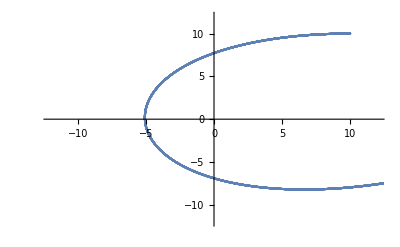

```mathematica
OneParticleData = TimeEvolveRK4[OneParticle,{{0.001}},0,0.01,nsteps,1,a,"ClassicalNBody"];
xyplot=Table[{OneParticleData[[j,2,1,1,1]],OneParticleData[[j,2,1,1,2]]},{j,1,nsteps}];
pltrng=12;
ListPlot[{xyplot},PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}}]
```

```mathematica
TwoParticles = {{{7.,0.},{0.,0.4}},{{8.,0.},{0,.3}}};
mjze = {{0.001},{0.001}};
```

```mathematica
TwoParticledata = TimeEvolveRK4[TwoParticles,mjze,0,0.01,25000,1,a];
```

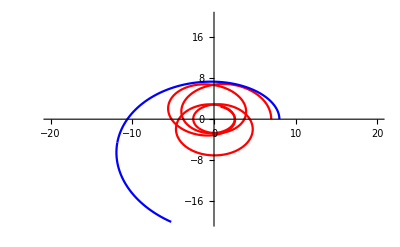

```mathematica
pltrng=20;
xyplot1=ListLinePlot[Table[{TwoParticledata[[j,2,1,1,1]],TwoParticledata[[j,2,1,1,2]]},{j,1,Length[TwoParticledata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Red}];
xyplot2 = ListLinePlot[Table[{TwoParticledata[[j,2,2,1,1]],TwoParticledata[[j,2,2,1,2]]},{j,1,Length[data]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Blue}];
Show[{xyplot1,xyplot2}]
```

```mathematica
TwoParticleMasslessdata = TimeEvolveRK4[TwoParticles,{{0.},{0.}},0,0.01,25000,1,a];
```

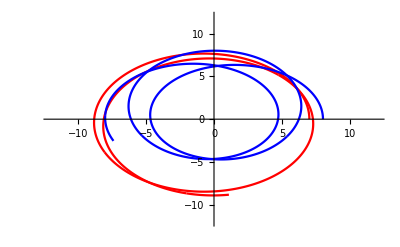

```mathematica
xyplot3=ListLinePlot[Table[{TwoParticleMasslessdata[[j,2,1,1,1]],TwoParticleMasslessdata[[j,2,1,1,2]]},{j,1,Length[TwoParticleMasslessdata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Red}];
xyplot4 = ListLinePlot[Table[{TwoParticleMasslessdata[[j,2,2,1,1]],TwoParticleMasslessdata[[j,2,2,1,2]]},{j,1,Length[TwoParticleMasslessdata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Blue}];
Show[{xyplot3,xyplot4}]
```

```mathematica
ThreeParticles = {{{7.,0.},{0.,.4}},{{8.,0.},{0.,.3}},{{9.,0},{0.,.25}}};
ThreeMasses = {{0.001},{0.001},{0.001}};
```

```mathematica
ThreeParticledata = TimeEvolveRK4[ThreeParticles,ThreeMasses,0,0.01,25000,1,a];
```

```mathematica
pltrng=12;
```

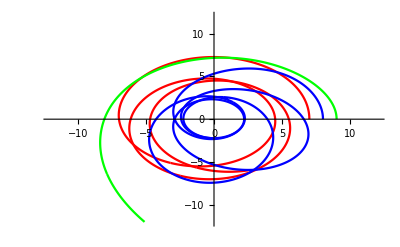

```mathematica
xyplot5=ListLinePlot[Table[{ThreeParticledata[[j,2,1,1,1]],ThreeParticledata[[j,2,1,1,2]]},{j,1,Length[ThreeParticledata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Red}];
xyplot6 = ListLinePlot[Table[{ThreeParticledata[[j,2,2,1,1]],ThreeParticledata[[j,2,2,1,2]]},{j,1,Length[ThreeParticledata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Blue}];
xyplot7 = ListLinePlot[Table[{ThreeParticledata[[j,2,3,1,1]],ThreeParticledata[[j,2,3,1,2]]},{j,1,Length[ThreeParticledata]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{Green}];
Show[{xyplot5,xyplot6,xyplot7}]
```

```mathematica
MakeLotsOfInitialConditions[nparticles_]:=Module[{vecs,masses,r,phi,phid,i},
vecs = Table[{0.},nparticles];
For[i=1,i≤nparticles,i++,
r = RandomReal[{5,10}];
phi = RandomReal[{0,2Pi}];
phid = RandomReal[{0.02,0.1}];
vecs[[i]] = {{r*Cos[phi],r*Sin[phi]},{-r*Sin[phi]phid,r*Cos[phi]phid}};
];
masses = Table[{0.001},nparticles];
Return[{vecs,masses}];
]
```

```mathematica
CalcNPlot[nparticles_]:=Module[{InitVecs,InitMasses,conditions,data,i,plot,plotlist,pltrng,colors,fname},
conditions = MakeLotsOfInitialConditions[nparticles];
InitVecs = conditions[[1]];
InitMasses = conditions[[2]];
data = TimeEvolveRK4[InitVecs,InitMasses,0,0.01,250,1,a,"ClassicalNBody"];
fname = "/Users/alexdeich/thesis/code/mine/nbody_output/"<>ToString[DateList[][[2]]]<>"_"<>ToString[DateList[][[3]]]<>"_"<>ToString[nparticles]<>"_nbody.csv";
Export[fname,data];
plotlist = Table[{0.},nparticles];
pltrng= 20;
colors = {Red,Blue,Green,Black,Orange,Pink,Purple,Yellow,Cyan,Magenta,Brown,Gray};
For[i=1,i≤nparticles,i++,
plot = ListPlot[Table[{data[[j,2,i,1,1]],data[[j,2,i,1,2]]},{j,1,Length[data]}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{colors[[Mod[i,Length[colors]+1]]]}];
plotlist[[i]]=plot;
];
Return[plotlist];
]
```

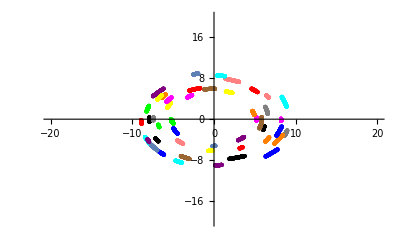

```mathematica
Show[CalcNPlot[50]]
```

To a certain extent, I don’t know why this works.  I edited xy2radMotion to output the “correct” velocity and acceleration vectors (that is, v={rd,r*td}, a={rdd-rtd^2,r*tdd+2rd*td}), but it didn’t give me the right result.  What did work was to use {rd,td} for velocity and the “correct” vector for acceleration.  Why does this work? Not sure:  maybe because you only use the velocity vector for the initial conditions, but the acceleration  is for the derivative vector? This suggests that if you were to time-evolve some system in polar coordinates, you would time-evolve the {rd,td} vector by the “correct” acceleration vector.  Ah ha! perhaps if you time evolve the {r,t} vector you would need the “correct” velocity vector as well.  perhaps.